# cutoff functions

## check the behaviour of exponential cutoff

## just cutoff stuff

```mathematica
Ω=1;
```

```mathematica
cExp[ε_,k_]:=ⅇ^(-ε*Abs[k])
cSharp[ε_,k_]:=HeavisideTheta[k+ε,-k+ε]
```

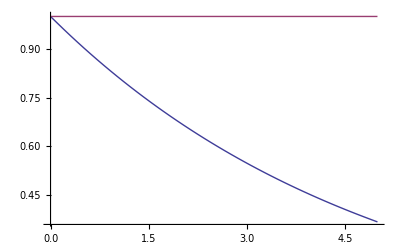

```mathematica
Plot[{cExp[1/(5*Ω),k],cSharp[5*Ω,k]},{k,0,5}]
```

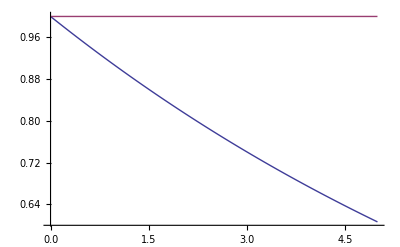

```mathematica
Plot[{cExp[1/(10*Ω),k],cSharp[5*Ω,k]},{k,0,5}]
```

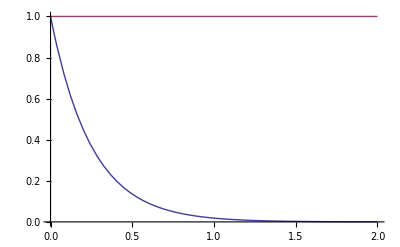

```mathematica
Plot[{cExp[1/(2.5*Ω),k],cSharp[1/(5*Ω),k]},{k,0,2}]
```

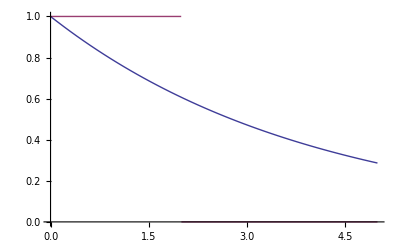

```mathematica
Plot[{cExp[1/(40*Ω),k],cSharp[1/(5*Ω),k]},{k,0,5}]
```

## fourier transforms + cutoffs

### lorentzian

```mathematica
fL[x_,σ_]:=σ/π 1/(x^2+σ^2)
ftilL[k_,σ_]:=FourierTransform[fL[x,σ],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

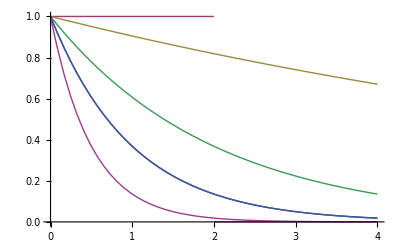

```mathematica
Plot[{cExp[1/(10*Ω),k],cSharp[1/(5*Ω),k],ftilL[k,0.1],ftilL[k,0.5],ftilL[k,1],ftilL[k,2]},{k,0,4}]
```

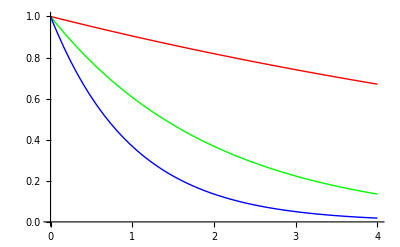

```mathematica
Plot[{ftilL[k,0.1],ftilL[k,0.5],ftilL[k,1]},{k,0,4},
PlotStyle->{Red,Green,Blue}]
```

### gaussian

```mathematica
fG[x_,σ_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftilG[k_,σ_]:=FourierTransform[fG[x,σ],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

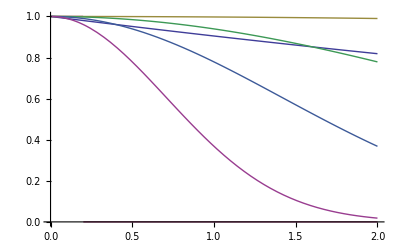

```mathematica
Plot[{cExp[1/(10*Ω),k],cSharp[1/(5*Ω),k],ftilG[k,0.1],ftilG[k,0.5],ftilG[k,1],ftilG[k,2]},{k,0,2}]
```

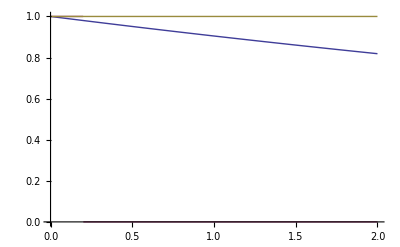

```mathematica
Plot[{cExp[1/(10*Ω),k],cSharp[1/(5*Ω),k],ftilG[k,10^-4/Ω]},{k,0,2}]
```

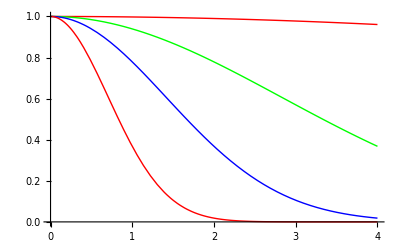

```mathematica
Plot[{ftilG[k,0.1],ftilG[k,0.5],ftilG[k,1],ftilG[k,2]},{k,0,4},
PlotStyle->{Red,Green,Blue}]
```